# Electrostatic potential and reorganization energy for arbitrary charge distributions near metal electrode covered with dielectric

## Spherical and cylindrical cavities

## Units

```mathematica
bohr2a=0.529177`10;
a2bohr=1/bohr2a;
au2kcal=627.5095`10;
kcal2au=1/au2kcal;
ev2cm=8065.54477`10;
cm2ev = 1/ev2cm ;
au2ev=27.2113`10;
ev2au = 1/au2ev;
cm2au=cm2ev*ev2au;     
au2cm=1/cm2au;
kcal2ev=kcal2au*au2ev;
ev2kcal=1/kcal2ev;
```

## Parameters

Dielectric permittivities:
solvent: ϵ_s
SAM: ϵ_m

Geometry:
R - Radius of a shperical cavity around the charge
d - distance from the charge to the electrode surface.

```mathematica
ϵs=78.0;
ϵsinf=1.8;
```

```mathematica
ϵm=2.25;
ϵminf=2.25;
```

## Model

### Spherical cavity

```mathematica
Graphics3D[{
{Opacity[0.5],Sphere[{0,0,0},0.75]},
{LightBlue,Opacity[0.5],Cuboid[{-1,-1,1.0},{1,1,1.5}]},
{Pink,Opacity[0.5],Cuboid[{-1,-1,1.5},{1,1,2.5}]},
{Opacity[0.0],Cuboid[{-1,-1,-1},{1,1,1.5}]},
{Text["I (ϵ_s)",{-0.9,1,-0.9},{-1,0}]},
{Text["II (ϵ_m)",{-0.9,1,1.1},{-1,0}]},
{Text["III (ϵ=∞)",{-0.9,1,1.6},{-1,0}]},
{Arrowheads[0.02],Arrow[{{-1.5,0,0},{1.5,0,0}}]},
{Text["x",{1.55,0,-0.05}]},
{Arrowheads[0.02],Arrow[{{0,-1.5,0},{0,1.5,0}}]},
{Text["y",{0,1.55,0.05}]},
{Arrowheads[0.02],Arrow[{{0,0,-1.5},{0,0,3.0}}]},
{Text["z",{-0.05,0.25,3.0}]},
{Text["0",{-0.05,0.05,-0.05}]},
{PointSize[Tiny],Point[Table[{0,0.75Cos[(2π(i-1))/200],0.75Sin[(2π(i-1))/200]},{i,1,201}]]},
{PointSize[Tiny],Point[Table[{0.75Cos[(2π(i-1))/200],0,0.75Sin[(2π(i-1))/200]},{i,1,201}]]},
{PointSize[Tiny],Point[Table[{0.75Cos[(2π(i-1))/200],0.75Sin[(2π(i-1))/200],0},{i,1,201}]]},
{Point[{0,0,0.75}]},
{Point[{0,0.75,0}]},
{Point[{0.75,0,0}]},
{Point[{0,0,-0.75}]},
{Point[{0,-0.75,0}]},
{Point[{-0.75,0,0}]},
{Point[{0,0,1}]},
{Point[{0,0,1.5}]},
{Text["R",{-0.05,0.1,0.80}]},
{Text["d",{-0.05,0.1,1.0}]},
{Text["d+δ",{-0.05,0.1,1.5}]}
},Boxed->False,ImageSize->Large,ViewPoint->{2,10,-1}]
```

-Graphics3D-

### Cylindrical Cavity

```mathematica
Graphics3D[{
{Green,Opacity[0.4],Sphere[{0,0,0},0.75]},
{White,Opacity[0.2],Cylinder[{{0,0,-0.75},{0,0,1.49}},0.75]},
{Orange,Opacity[0.4],Cuboid[{-1,-1,1.51},{1,1,2.5}]},
{Blue,Opacity[0.1],Cuboid[{-1,-1,-1.5},{1,1,1.5}]},
{Text["ε = 78",{-0.8,1,-0.9},{-1,0}]},
{Text["ε = ∞",{-0.8,1,1.6},{-1,0}]},
{Arrowheads[0.02],Arrow[{{0,0,-1.75},{0,0,3.5}}]},
{Text["z",{-0.05,0.25,3.5}]},
{PointSize[Tiny],Point[Table[{0.75Cos[(2π(i-1))/200],0.75Sin[(2π(i-1))/200],0},{i,1,201}]]},
{Black,PointSize[Large],Point[{0,0,0}]},
{Black,PointSize[Large],Point[{0,0,1.5}]}
},Boxed->False,ImageSize->Large,ViewPoint->{2,10,-1},BaseStyle->14]
```

-Graphics3D-

```mathematica
Graphics3D[{
{Green,Opacity[0.5],Sphere[{0,0,0},0.75]},
{White,Opacity[0.2],Cylinder[{{0,0,-0.75},{0,0,1.5}},0.75]},
{Orange,Opacity[0.5],Cuboid[{-1,-1,1.5},{1,1,2.5}]},
{Blue,Opacity[0.1],Cuboid[{-1,-1,-1.5},{1,1,1.5}]},
{Text["ε = 78",{-0.8,1,-0.9},{-1,0}]},
{Text["ε = ∞",{-0.8,1,1.6},{-1,0}]},
{Arrowheads[0.02],Arrow[{{0,0,-1.75},{0,0,3.5}}]},
{Text["z",{-0.05,0.25,3.5}]},
{Text["Δq = -1",{-0.1,0.05,0.15},{-1,0}]},
{PointSize[Tiny],Point[Table[{0.75Cos[(2π(i-1))/200],0.75Sin[(2π(i-1))/200],0},{i,1,201}]]},
{Black,PointSize[Large],Point[{0,0,0}]},
{Black,PointSize[Large],Point[{0,0,1.5}]},
{Text["d",{-0.1,0.1,1.5}]}
},Boxed->False,ImageSize->Large,ViewPoint->{2,10,-1},BaseStyle->14]
```

-Graphics3D-

```mathematica
Graphics3D[{
{Opacity[0.5],Cylinder[{{0,0,-0.75},{0,0,0.75}},0.75]},
{LightBlue,Opacity[0.5],Cuboid[{-1,-1,1.0},{1,1,1.5}]},
{Pink,Opacity[0.5],Cuboid[{-1,-1,1.5},{1,1,2.5}]},
{Opacity[0.0],Cuboid[{-1,-1,-1},{1,1,1.5}]},
{Text["I (ϵ_s)",{-0.9,1,-0.9},{-1,0}]},
{Text["II (ϵ_m)",{-0.9,1,1.1},{-1,0}]},
{Text["III (ϵ=∞)",{-0.9,1,1.6},{-1,0}]},
{Arrowheads[0.02],Arrow[{{-1.5,0,0},{1.5,0,0}}]},
{Text["x",{1.55,0,-0.05}]},
{Arrowheads[0.02],Arrow[{{0,-1.5,0},{0,1.5,0}}]},
{Text["y",{0,1.55,0.05}]},
{Arrowheads[0.02],Arrow[{{0,0,-1.5},{0,0,3.0}}]},
{Text["z",{-0.05,0.25,3.0}]},
{Text["0",{-0.05,0.05,-0.05}]},
{PointSize[Tiny],Point[Table[{0.75Cos[(2π(i-1))/200],0.75Sin[(2π(i-1))/200],0},{i,1,201}]]},
{Point[{0,0,0.75}]},
{Point[{0,0.75,0}]},
{Point[{0.75,0,0}]},
{Point[{0,0,-0.75}]},
{Point[{0,-0.75,0}]},
{Point[{-0.75,0,0}]},
{Point[{0,0,1}]},
{Point[{0,0,1.5}]},
{Text["L/2",{-0.05,0.1,0.80}]},
{Text["d",{-0.05,0.1,1.0}]},
{Text["d+δ",{-0.05,0.1,1.5}]}
},Boxed->False,ImageSize->Large,ViewPoint->{2,10,-1}]
```

-Graphics3D-

## Coordinate transformations

```mathematica
CylindricalToSpherical[cyl_]:=Module[{ρ,x,y,z,r,θ,ϕ},
ρ=cyl⟦1⟧;
ϕ=cyl⟦2⟧;
z=cyl⟦3⟧;
r=√(ρ^2+z^2);
θ=If[z==0,π/2,ArcCos[z/(√(z^2+ρ^2))]];
{r,θ,ϕ}
];
```

```mathematica
CylindricalToSpherical[{0,0,0}]
```

{0,π/2,0}

```mathematica
SphericalToCylindrical[sph_]:=Module[{r,θ,ϕ,ρ,z},
r=sph⟦1⟧;
θ=sph⟦2⟧;
ϕ=sph⟦3⟧;
ρ=r Sin[θ];
z=r Cos[θ];
{ρ,ϕ,z}
];
```

```mathematica
CartesianToSpherical[xyz_]:=Module[{x,y,z,r,θ,ϕ},
x=xyz⟦1⟧;
y=xyz⟦2⟧;
z=xyz⟦3⟧;
r=√(x^2+y^2+z^2);
θ=If[z==0,π/2,ArcCos[z/r]];
ϕ=Which[
y==0,0,
x==0,π/2,
True,ArcTan[y/x]
];
{r,θ,ϕ}
];
```

```mathematica
CartesianToCylindrical[xyz_]:=Module[{x,y,z,ρ,ϕ,zc},
x=xyz⟦1⟧;
y=xyz⟦2⟧;
z=xyz⟦3⟧;
ρ=√(x^2+y^2);
ϕ=Which[
x==0&&y==0,0,
x>=0,ArcSin[y/ρ],
x<0,-ArcSin[y/ρ]+π
];
{ρ,ϕ,z}
];
```

```mathematica
CylindricalToCartesian[cyl_]:=Module[{ρ,ϕ,z,x,y},
ρ=cyl⟦1⟧;
ϕ=cyl⟦2⟧;
z=cyl⟦3⟧;
x=ρ Cos[ϕ];
y=ρ Sin[ϕ];
{x,y,z}
];
```

```mathematica
CartesianToCylindrical[{0,0,0}]
```

{0,0,0}

```mathematica
CartesianToSpherical[{0,0,0}]
```

{0,π/2,0}

## Polarization induced potentials (region I)

ρ is a nested list of the following structure:
Table[ { q_i, {x_i,y_i,z_i} }, {i, 1, N} ]

### Potential from the charge distribution ρ itself

```mathematica
Φ1[ϵ_,ρ_,{r_,ϕ_,z_}]:=Module[
{κ,nCharges,pot,Q,xyzi,xyz,dist},
nCharges=Length[ρ];
pot=0;
Do[
Q=ρ⟦i,1⟧;
xyzi=ρ⟦i,2⟧;
xyz=CoordinateTransform["Cylindrical"->"Cartesian",{r,ϕ,z}];
dist=Norm[xyz-xyzi]a2bohr;
pot+=Q/dist,
{i,1,nCharges}];
pot/ϵ
];
```

### Potentials from the image charges (polarization potentials)

```mathematica
Φ23[d_,δ_,ϵs_,ϵm_,ρ_,cylcoord_,OptionsPattern[{NS->100}]]:=Module[
{NN,κ,nCharges,pot,Q,xyz,xyzi,di,cylcoordi,ri,ϕi,zi,Φ2,Φ3},
NN=OptionValue[NS];
κ=(ϵm-ϵs)/(ϵm+ϵs);
nCharges=Length[ρ];
pot=0;
Do[
Q=ρ⟦i,1⟧;
xyzi=ρ⟦i,2⟧;
xyz=CylindricalToCartesian[cylcoord];
di=d-xyzi⟦3⟧;
cylcoordi=CartesianToCylindrical[xyz-xyzi];
ri=cylcoordi⟦1⟧;
ϕi=cylcoordi⟦2⟧;
zi=cylcoordi⟦3⟧;
Φ2=If[κ==0,-Q 1/(a2bohr √(ri^2+(2di-zi)^2)),-Q Sum[(-κ)^n/(a2bohr √(ri^2+(2n δ+2di-zi)^2)),{n,0,NN}]];
Φ3=If[κ==0,-Q 1/(a2bohr √(ri^2+(2 δ+2di-zi)^2)),-Q Sum[(-κ)^n/(a2bohr √(ri^2+((2n+2) δ+2di-zi)^2)),{n,0,NN}]];
pot+=κ/ϵs Φ2+1/ϵs Φ3,
{i,1,nCharges,1}];
pot
];
```

```mathematica
Φ23[5.0,1.0,ϵs,ϵm,{{1,{0,0,0}}},{5.0,π/2,π/3},NS->300]
```

0.000167021

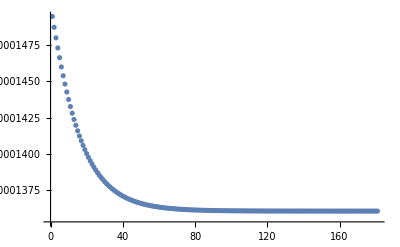

```mathematica
ListPlot[Table[Φ23[5.0,1,ϵs,ϵm,{{1,{0,0,0}}},{5,0,0},NS->i],{i,20,200}],PlotRange->All]
```

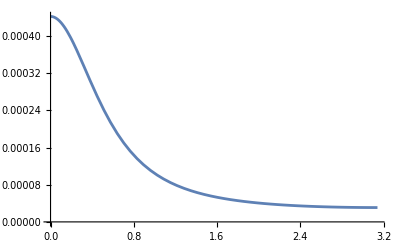

```mathematica
Plot[Φ23[5.0,1,ϵs,ϵm,{{-1,{0,0,-1}},{1,{0,0,1}}},SphericalToCylindrical[{5.0,θ,0}]],{θ,0,π}]
```

```mathematica
Φmin=Φ23[5.0,1,ϵs,ϵm,{{1,{0,0,1}}},SphericalToCylindrical[{5.0,π,0}]]
```

0.0000763099

```mathematica
Φmax=Φ23[5.0,1,ϵs,ϵm,{{1,{0,0,1}}},SphericalToCylindrical[{5.0,0,0}]]
```

0.000945237

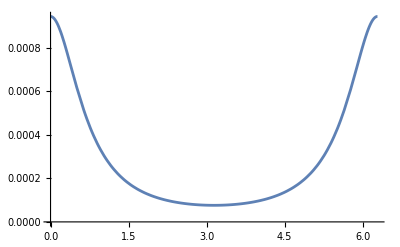

```mathematica
Plot[Φ23[5.0,1,ϵs,ϵm,{{1,{0,0,1}}},SphericalToCylindrical[{5.0,θ,-π}]],{θ,0,2π}]
```

```mathematica
SphericalPlot3D[5,{θ,0,π/2},{ϕ,0,2π},Mesh->Full,Axes->True]
```

-Graphics3D-

```mathematica
dtmp:=SphericalPlot3D[5,{θ,0,π},{ϕ,0,2π},Mesh->Full,Axes->True,ImageSize->Large,
ColorFunction->(ColorData["TemperatureMap"][(Φ23[5.0,1,ϵs,ϵm,{{1,{0,0,1}}},SphericalToCylindrical[{5,#4,#5}]]-Φmin)/(Φmax-Φmin)]&),
ColorFunctionScaling->False,
Mesh->Full,PlotPoints->20
];
Button["Show potential on the surface of a sphere",CreateWindow[DocumentNotebook[{dtmp}]]]
```

Show potential on the surface of a sphere

## Reorganization energy

### Exact expressions for the collection of point charges λ=-1/2∫Δρ[Δϕ(ε_0)-Δϕ(ε_∞)]ⅆV

```mathematica
λexact[R_,d_,δ_,ϵs_,ϵsinf_,ϵm_,ϵminf_,ρi_,ρf_,OptionsPattern[{NS->100}]]:=Module[
{dQtot,nCharges,nChargesi,nChargesf,Sc,dΦtot,dΦinf,dΦav,dρ,dρi,λ,dqi,xyz,xyzi,di},
nChargesi=Length[ρi];
nChargesf=Length[ρf];
If[nChargesi!=nChargesf,
Print["Numbers of initial and final point charges do not match! Abort..."];Abort[],
nCharges=nChargesi
];
dρ=Table[{ρf⟦i,1⟧-ρi⟦i,1⟧,ρi⟦i,2⟧},{i,1,nCharges}];
dQtot=Sum[dρ⟦i,1⟧,{i,1,nCharges}];
If[dQtot==0,Print["Warning: Total charge of Δρ is zero!"]];
Sc=4π R^2 a2bohr^2;
λ=0;
Do[
dqi=dρ⟦i,1⟧;
xyzi=dρ⟦i,2⟧;
di=d-xyzi⟦3⟧;
dρi=Join[Table[{dρ⟦k,1⟧,dρ⟦k,2⟧-xyzi},{k,1,i-1}],Table[{dρ⟦k,1⟧,dρ⟦k,2⟧-xyzi},{k,i+1,nCharges}]];
(*dρi=Join[Table[{dρ⟦k,1⟧,dρ⟦k,2⟧-xyzi},{k,1,nCharges}]];*)
dΦtot=Φ23[di,δ,ϵs,ϵm,dρi, {0,0,0},NS->OptionValue[NS]];
dΦinf=Φ23[di,δ,ϵsinf,ϵminf,dρi, {0,0,0},NS->OptionValue[NS]];
λ+=dqi(dΦtot-dΦinf),
{i,1,nCharges}
];
-1/2 λ au2kcal
];
```

### Averaging over spherical cavity with radius R

```mathematica
λsphav[R_,d_,δ_,ϵs_,ϵsinf_,ϵm_,ϵminf_,ρi_,ρf_,OptionsPattern[{NS->100}]]:=Module[
{dQtot,nCharges,Sc,dΦtot,dΦinf,dΦav,dρ},
nCharges=Length[ρi];
dρ=Table[{ρf⟦i,1⟧-ρi⟦i,1⟧,ρi⟦i,2⟧},{i,1,nCharges}];
dQtot=Sum[dρ⟦i,1⟧,{i,1,nCharges}];
If[dQtot==0,
Print["Total charge of Δρ is zero!"];0,
Sc=4π R^2 a2bohr^2;
dΦtot=a2bohr^2 R^2 NIntegrate[(Φ1[ϵs,dρ,SphericalToCylindrical[{R,θ,ϕ}]]+Φ23[d,δ,ϵs,ϵm,dρ,SphericalToCylindrical[{R,θ,ϕ}],NS->OptionValue[NS]])Sin[θ],{θ,0,π},{ϕ,-π,π}];
dΦinf=a2bohr^2 R^2 NIntegrate[(Φ1[ϵsinf,dρ,SphericalToCylindrical[{R,θ,ϕ}]]+Φ23[d,δ,ϵsinf,ϵminf,dρ,SphericalToCylindrical[{R,θ,ϕ}],NS->OptionValue[NS]])Sin[θ],{θ,0,π},{ϕ,-π,π}];
dΦav=(dΦtot-dΦinf)/Sc;
(* Print["Average potential on the sphere: ",dΦav," a.u."]; *)
-1/2 dQtot dΦav au2kcal]
];
```

Check against Liu-Newton Fig. 2 in  J. Phys. Chem. 1994, 98, 7162–7169:

```mathematica
ρi={{1,{0,0,0}}};
ρf={{2,{0,0,0}}};
λ33=ParallelTable[{L,kcal2ev×λsphav[3.3,3.3,L,78,1.8,2.25,2.25,ρi,ρf]},{L,0,60,2},Method->"FinestGrained"];
λ38=ParallelTable[{L,kcal2ev×λsphav[3.8,3.8,L,78,1.8,2.25,2.25,ρi,ρf]},{L,0,60,2},Method->"FinestGrained"];
λ43=ParallelTable[{L,kcal2ev×λsphav[4.3,4.3,L,78,1.8,2.25,2.25,ρi,ρf]},{L,0,60,2},Method->"FinestGrained"];
```

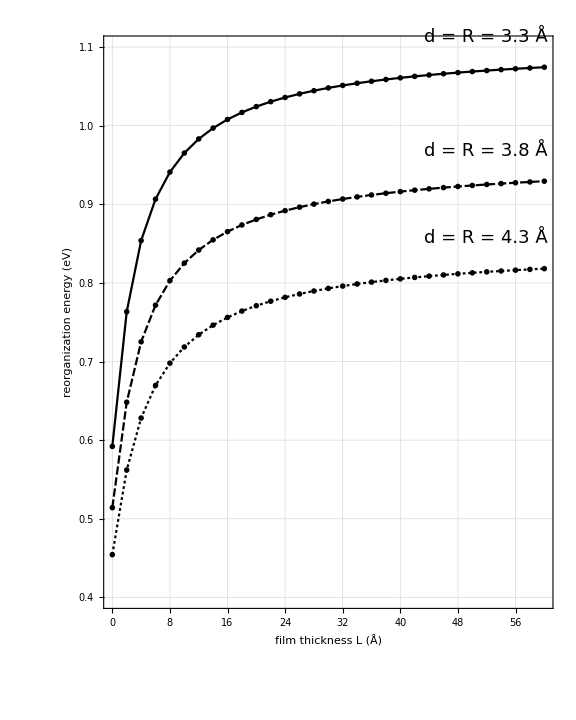

```mathematica
ListLinePlot[{λ33,λ38,λ43},
PlotRange->{{0,60},{0.4,1.1}},
GridLines->Automatic,
Axes->False,Frame->True,
BaseStyle->{18},
FrameStyle->Directive[Black,Thick,18],
ImageSize->Large,AspectRatio->1.25,
PlotLabels->Placed[{"d = R = 3.3 Å ","d = R = 3.8 Å ","d = R = 4.3 Å "},{{Scaled[3],Before}}],
PlotTheme->"Monochrome",
FrameLabel->{"film thickness L (Å)","reorganization energy (eV)"}
]
```

### Averaging over cylindrical cavity with radius R and length L

```mathematica
λcylav[R_,L_,d_,δ_,ϵs_,ϵsinf_,ϵm_,ϵminf_,ρi_,ρf_,OptionsPattern[{NS->100}]]:=Module[{dQtot,nCharges,Sc,dΦtotface1,dΦtotface2,dΦtotfaces,dΦtotside,dΦinfface1,dΦinfface2,dΦinffaces,dΦinfside,dΦtot,dΦinf,dΦav,dρ},
nCharges=Length[ρi];
dρ=Table[{ρf⟦i,1⟧-ρi⟦i,1⟧,ρi⟦i,2⟧},{i,1,nCharges}];
dQtot=Sum[dρ⟦i,1⟧,{i,1,nCharges}];
If[dQtot==0,
Print["Total charge of Δρ is zero!"];0,
Sc=2π R (L+R)a2bohr^2;
dΦtotface1=a2bohr^2 NIntegrate[(Φ1[ϵs,dρ,{ρ,ϕ,-L/2}]+Φ23[d,δ,ϵs,ϵm,dρ,{ρ,ϕ,-L/2},NS->OptionValue[NS]])ρ,{ρ,0,R},{ϕ,-π,π}];
dΦtotface2=a2bohr^2 NIntegrate[(Φ1[ϵs,dρ,{ρ,ϕ,L/2}]+Φ23[d,δ,ϵs,ϵm,dρ,{ρ,ϕ,L/2},NS->OptionValue[NS]])ρ,{ρ,0,R},{ϕ,-π,π}];
dΦtotfaces=dΦtotface1+dΦtotface2;
dΦtotside=a2bohr^2 R NIntegrate[(Φ1[ϵs,dρ,{R,ϕ,z}]+Φ23[d,δ,ϵs,ϵm,dρ,{R,ϕ,z},NS->OptionValue[NS]]),{z,-L/2,L/2},{ϕ,-π,π}];
dΦtot=dΦtotfaces+dΦtotside;

dΦinfface1=a2bohr^2 NIntegrate[(Φ1[ϵsinf,dρ,{ρ,ϕ,-L/2}]+Φ23[d,δ,ϵsinf,ϵminf,dρ,{ρ,ϕ,-L/2},NS->OptionValue[NS]])ρ,{ρ,0,R},{ϕ,-π,π}];
dΦinfface2=a2bohr^2 NIntegrate[(Φ1[ϵsinf,dρ,{ρ,ϕ,L/2}]+Φ23[d,δ,ϵsinf,ϵminf,dρ,{ρ,ϕ,L/2},NS->OptionValue[NS]])ρ,{ρ,0,R},{ϕ,-π,π}];
dΦinffaces=dΦinfface1+dΦinfface2;
dΦinfside=a2bohr^2 R NIntegrate[(Φ1[ϵsinf,dρ,{R,ϕ,z}]+Φ23[d,δ,ϵsinf,ϵminf,dρ,{R,ϕ,z},NS->OptionValue[NS]]),{z,-L/2,L/2},{ϕ,-π,π}];
dΦinf=dΦinffaces+dΦinfside;

dΦav=(dΦtot-dΦinf)/Sc;
(* Print["Average potential on the cylinder surface: ",dΦav," a.u."]; *)
-1/2 dQtot dΦav au2kcal]
];
```

## Cavity parameters for (Zr-bridge)-Ru(III/II)-OH/H2O systems

Inner-sphere reorganization energies (kcal/mol):

```mathematica
λinET=3.9;
λinPCET=13.4;
```

Bridge lengths for n=1, 2, 3:

```mathematica
bridgeL={7.4,17.,26.}; (* UNC: crystal structures *)
bridgeLmy={10.21,17.45,23.36}; (* from DFT/PCM optimizations of the bridge units *)
```

“Experimental” apparent reorganization energies:

```mathematica
λETUNCvsL=MapAt[#×ev2kcal&,{{7.4,0.38},{17,0.72},{26,0.72}},{All,2}];
λPCETUNCvsL=MapAt[#×ev2kcal&,{{7.4,0.91},{17,0.97},{26,0.88}},{All,2}];
```

ET: Cavity surface areas from PCM calculations of Ru-tpy-bpy complexes (in Å^2):

```mathematica
SETreactant=550.872;
VETreactant=705.72;
SETproduct=552.315;
SPCETreactant=548.896;
SPCETproduct=552.308;
```

Cavity volumes from PCM calculations (Gaussian 16):

```mathematica
VETreactant=705.72;
VETproduct=707.421;
VPCETreactant=701.861;
VPCETproduct=707.421;
VPCETwithdonorreactant=734.607;
VPCETwithdonorproduct=736.342;
VPCETwithdonor2reactant=789.664;
VPCETwithdonor2product=793.485;
```

Radii of spherical cavities with the same surface areas:

```mathematica
RETreactant=((3VETreactant)/(4π))^(1/3);
RETproduct=1/2 √(SETproduct/π);
RPCETreactant=1/2 √(SPCETreactant/π);
RPCETproduct=1/2 √(SPCETproduct/π);
```

Radii of spherical cavities with the same volumes:

```mathematica
RVETreactant=((3VETreactant)/(4π))^(1/3)
RVETproduct=((3VETproduct)/(4π))^(1/3)
RVPCETreactant=((3VPCETreactant)/(4π))^(1/3)
RVPCETproduct=((3VPCETproduct)/(4π))^(1/3)
RVPCETwithdonorreactant=((3VPCETwithdonorreactant)/(4π))^(1/3)
RVPCETwithdonorproduct=((3VPCETwithdonorproduct)/(4π))^(1/3)
RVPCETwithdonor2reactant=((3VPCETwithdonor2reactant)/(4π))^(1/3)
RVPCETwithdonor2product=((3VPCETwithdonor2product)/(4π))^(1/3)
```

5.52308

5.52751

5.51299

5.52751

5.59743

5.60184

5.73391

5.74315

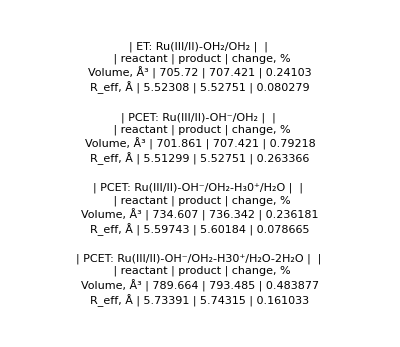

```mathematica
GraphicsColumn[{
Grid[
{
{"","ET: Ru(III/II)-OH_2/OH_2",SpanFromLeft},
{"","reactant","product","change, %"},
{"Volume, Å^3",VETreactant,VETproduct,(VETproduct-VETreactant)/VETreactant×100},
{"R_eff, Å",RVETreactant,RVETproduct,(RVETproduct-RVETreactant)/RVETreactant×100}
},
Dividers->All
],
Grid[
{
{"","PCET: Ru(III/II)-OH^-/OH_2",SpanFromLeft},
{"","reactant","product","change, %"},
{"Volume, Å^3",VPCETreactant,VPCETproduct,(VPCETproduct-VPCETreactant)/VPCETreactant×100},
{"R_eff, Å",RVPCETreactant,RVPCETproduct,(RVPCETproduct-RVPCETreactant)/RVPCETreactant×100}
},
Dividers->All
],
Grid[
{
{"","PCET: Ru(III/II)-OH^-/OH_2-H_30^+/H_2O",SpanFromLeft},
{"","reactant","product","change, %"},
{"Volume, Å^3",VPCETwithdonorreactant,VPCETwithdonorproduct,(VPCETwithdonorproduct-VPCETwithdonorreactant)/VPCETwithdonorreactant×100},
{"R_eff, Å",RVPCETwithdonorreactant,RVPCETwithdonorproduct,(RVPCETwithdonorproduct-RVPCETwithdonorreactant)/RVPCETwithdonorreactant×100}
},
Dividers->All
],
Grid[
{
{"","PCET: Ru(III/II)-OH^-/OH_2-H30^+/H_2O-2H_2O",SpanFromLeft},
{"","reactant","product","change, %"},
{"Volume, Å^3",VPCETwithdonor2reactant,VPCETwithdonor2product,(VPCETwithdonor2product-VPCETwithdonor2reactant)/VPCETwithdonor2reactant×100},
{"R_eff, Å",RVPCETwithdonor2reactant,RVPCETwithdonor2product,(RVPCETwithdonor2product-RVPCETwithdonor2reactant)/RVPCETwithdonor2reactant×100}
},
Dividers->All
]
}
]
```

```mathematica
Grid[
{
{"","ET: Ru(III/II)-OH_2/OH_2",SpanFromLeft,"PCET: Ru(III/II)-OH^-/OH_2",SpanFromLeft,"PCET: Ru(III/II)-OH^-/OH_2-H_30^+/H_2O",SpanFromLeft,"PCET: Ru(III/II)-OH^-/OH_2-H30^+/H_2O-2H_2O",SpanFromLeft},
{"","reactant","product","reactant","product","reactant","product","reactant","product"},
{"Volume, Å^3",VETreactant,VETproduct,VPCETreactant,VPCETproduct,VPCETwithdonorreactant,VPCETwithdonorproduct,VPCETwithdonor2reactant,VPCETwithdonor2product},
{"R_eff, Å",RVETreactant,RVETproduct,RVPCETreactant,RVPCETproduct,RVPCETwithdonorreactant,RVPCETwithdonorproduct,RVPCETwithdonor2reactant,RVPCETwithdonor2product}
},
Dividers->All
]
```

| ET: Ru(III/II)-OH_2/OH_2 |  | PCET: Ru(III/II)-OH^-/OH_2 |  | PCET: Ru(III/II)-OH^-/OH_2-H_30^+/H_2O |  | PCET: Ru(III/II)-OH^-/OH_2-H30^+/H_2O-2H_2O | 
 | reactant | product | reactant | product | reactant | product | reactant | product
Volume, Å^3 | 705.72 | 707.421 | 701.861 | 707.421 | 789.664 | 793.485 | 789.664 | 793.485
R_eff, Å | 5.52308 | 5.52751 | 5.51299 | 5.52751 | 5.73391 | 5.74315 | 5.73391 | 5.74315

```mathematica
RVPCETwithdonorreactant/RVPCETreactant*100
```

104.007

Length of a cylindrical cavity accommodating bridge units:

```mathematica
cylL[bridgeL_]:=bridgeL+RETreactant;
```

```mathematica
λETUNCvsL
```

{{7.4,8.76304},{17,16.6036},{26,16.6036}}

```mathematica
xsphExp=λETUNCvsL⟦All,1⟧- RETreactant;
xcylExp=λETUNCvsL⟦All,1⟧- RETreactant;
```

## Single point charge at the center of a spherical cavity with the bridge described as a low-dielectric region (SAM)

```mathematica
ρETi={{3,{0,0,0}}};
ρETf={{2,{0,0,0}}};
```

```mathematica
λsphLtable=Monitor[
Table[{x+RETreactant,λsphav[RETreactant,RETreactant,x,ϵs,ϵsinf,ϵm,ϵminf,ρETi,ρETf,NS->100]},{x,0,35,0.5}],
ProgressIndicator[x/35]
];
```

```mathematica
λsphNoSAMLtable=Monitor[
Table[{x+RETreactant,λsphav[RETreactant,RETreactant,x,ϵs,ϵsinf,ϵs,ϵsinf,ρETi,ρETf,NS->100]},{x,0,35,0.5}],
ProgressIndicator[x/35]
];
```

```mathematica
λETsphLtable=MapAt[#+λinET&,λsphLtable,{All,2}];
λPCETsphLtable=MapAt[#+λinPCET&,λsphLtable,{All,2}];
λETsphNoSAMLtable=MapAt[#+λinET&,λsphNoSAMLtable,{All,2}];
λPCETsphNoSAMLtable=MapAt[#+λinPCET&,λsphNoSAMLtable,{All,2}];
```

```mathematica
λosphCalc=Thread[λsphav[RETreactant,RETreactant,xsphExp,ϵs,ϵsinf,ϵm,ϵminf,ρETi,ρETf,NS->100]]
λosphNoSAMCalc=Thread[λsphav[RETreactant,RETreactant,xsphExp,ϵs,ϵsinf,ϵs,ϵsinf,ρETi,ρETf,NS->100]]
```

{9.64475,12.7165,13.5703}

{10.2268,13.6651,14.5825}

```mathematica
Row[{
Grid[{
{"Spherical Cavity with SAM",SpanFromLeft},
{"","ET",SpanFromLeft,SpanFromLeft,"PCET",SpanFromLeft},
{"n",0,1,2,0,1,2},
Join[{"L"},bridgeL,bridgeL],
{"λ_in",λinET,SpanFromLeft,SpanFromLeft,λinPCET,SpanFromLeft},
Join[{"λ_o"},Thread@NumberForm[λosphCalc,3],Thread@NumberForm[λosphCalc,3]],
Join[{Style["λ_tot",Red,Bold]},Thread@NumberForm[λosphCalc+λinET,3],Thread@NumberForm[λosphCalc+λinPCET,3]],
Join[{Style["λ_app",Red,Bold]},Thread@NumberForm[λETUNCvsL⟦All,2⟧,3],Thread@NumberForm[λPCETUNCvsL⟦All,2⟧,3]]
},
Frame->All,
ItemStyle->Directive[FontSize->16],
Background->{None,{1->LightBlue,7->Yellow,8->LightPink}}],
Spacer[10],
Grid[{
{"Spherical Cavity without SAM",SpanFromLeft},
{"","ET",SpanFromLeft,SpanFromLeft,"PCET",SpanFromLeft},
{"n",0,1,2,0,1,2},
Join[{"L"},bridgeL,bridgeL],
{"λ_in",λinET,SpanFromLeft,SpanFromLeft,λinPCET,SpanFromLeft},
Join[{"λ_o"},Thread@NumberForm[λosphNoSAMCalc,3],Thread@NumberForm[λosphNoSAMCalc,3]],
Join[{Style["λ_tot",Red,Bold]},Thread@NumberForm[λosphNoSAMCalc+λinET,3],Thread@NumberForm[λosphNoSAMCalc+λinPCET,3]],
Join[{Style["λ_app",Red,Bold]},Thread@NumberForm[λETUNCvsL⟦All,2⟧,3],Thread@NumberForm[λPCETUNCvsL⟦All,2⟧,3]]
},
Frame->All,
ItemStyle->Directive[FontSize->16],
Background->{None,{1->LightBlue,7->Yellow,8->LightPink}}]
}]
```

Spherical Cavity with SAM |  |  |  |  |  | 
 | ET |  |  | PCET |  | 
n | 0 | 1 | 2 | 0 | 1 | 2
L | 7.4 | 17. | 26. | 7.4 | 17. | 26.
λ_in | 3.9 |  |  | 13.4 |  | 
λ_o | 9.64 | 12.7 | 13.6 | 9.64 | 12.7 | 13.6
λ_tot | 13.5 | 16.6 | 17.5 | 23. | 26.1 | 27.
λ_app | 8.76 | 16.6 | 16.6 | 21. | 22.4 | 20.3Spherical Cavity without SAM |  |  |  |  |  | 
 | ET |  |  | PCET |  | 
n | 0 | 1 | 2 | 0 | 1 | 2
L | 7.4 | 17. | 26. | 7.4 | 17. | 26.
λ_in | 3.9 |  |  | 13.4 |  | 
λ_o | 10.2 | 13.7 | 14.6 | 10.2 | 13.7 | 14.6
λ_tot | 14.1 | 17.6 | 18.5 | 23.6 | 27.1 | 28.
λ_app | 8.76 | 16.6 | 16.6 | 21. | 22.4 | 20.3

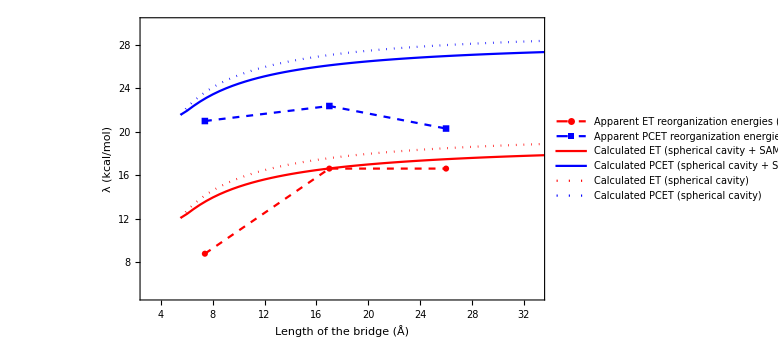

```mathematica
ListPlot[{λETUNCvsL,λPCETUNCvsL,λETsphLtable,λPCETsphLtable,λETsphNoSAMLtable,λPCETsphNoSAMLtable},
PlotRange->{{3,33},{5,30}},
BaseStyle->{FontSize->18},
ImageSize->Large,
Axes->False,
Frame->True,
FrameStyle->Directive[Black,Thickness[0.0025]],
PlotMarkers->{Automatic,Automatic,None,None,None,None},
Joined->True,
PlotStyle->{{Red,Dashed},{Blue,Dashed},Red,Blue,{Red,Dotted},{Blue,Dotted}},
FrameLabel->{"Length of the bridge (Å)","λ (kcal/mol)"},
LabelStyle->{12},
PlotLegends->Placed[
{"Apparent ET reorganization energies (UNC)",
"Apparent PCET reorganization energies (UNC)",
"Calculated ET (spherical cavity + SAM)",
"Calculated PCET (spherical cavity + SAM)",
"Calculated ET (spherical cavity)",
"Calculated PCET (spherical cavity)"},
{0.7,0.2}]
]
```

## Single point charge inside a cylindrical cavity with the bridge described as a part of the molecule

```mathematica
ρETcyli[bridgeL_]:={{3,{0,0,-(cylL[bridgeL]/2-RETreactant)}}};
ρETcylf[bridgeL_]:={{2,{0,0,-(cylL[bridgeL]/2-RETreactant)}}};
```

```mathematica
Monitor[
λcylLtable=Table[{x+RETreactant,λcylav[RETreactant,2×RETreactant+x,(2×RETreactant+x)/2,0,ϵs,ϵsinf,ϵm,ϵminf,ρETcyli[x],ρETcylf[x],NS->200]},{x,0,35,0.5}],
ProgressIndicator[x/35]
];
```

```mathematica
λETcylLtable=MapAt[#+λinET&,λcylLtable,{All,2}];
λPCETcylLtable=MapAt[#+λinPCET&,λcylLtable,{All,2}];
```

```mathematica
λocylCalc=Table[λcylav[RETreactant,2×RETreactant+x,(2×RETreactant+x)/2,0,ϵs,ϵsinf,ϵm,ϵminf,ρETcyli[x],ρETcylf[x],NS->200],{x,xcylExp}]
```

{4.87121,7.00492,6.67746}

```mathematica
Grid[{
{"Cylindrical Cavity",SpanFromLeft},
{"","ET",SpanFromLeft,SpanFromLeft,"PCET",SpanFromLeft},
{"n",0,1,2,0,1,2},
Join[{"L, Å"},bridgeL,bridgeL],
{"Reorganization energies, kcal/mol",SpanFromLeft},
{"","ET",SpanFromLeft,SpanFromLeft,"PCET",SpanFromLeft},
{"λ_in",λinET,SpanFromLeft,SpanFromLeft,λinPCET,SpanFromLeft},
Join[{"λ_o"},Thread@NumberForm[λocylCalc,3],Thread@NumberForm[λocylCalc,3]],
Join[{Style["λ_tot",Red,Bold]},Thread@NumberForm[λocylCalc+λinET,3],Thread@NumberForm[λocylCalc+λinPCET,3]],
Join[{Style["λ_app",Red,Bold]},Thread@NumberForm[λETUNCvsL⟦All,2⟧,3],Thread@NumberForm[λPCETUNCvsL⟦All,2⟧,3]]
},
Frame->All,
ItemStyle->Directive[FontSize->16],
Background->{None,{1->LightBlue,2->LightGray,5->LightGray,6->LightGray,9->Yellow,10->LightPink}}]
```

Cylindrical Cavity |  |  |  |  |  | 
 | ET |  |  | PCET |  | 
n | 0 | 1 | 2 | 0 | 1 | 2
L, Å | 7.4 | 17. | 26. | 7.4 | 17. | 26.
Reorganization energies, kcal/mol |  |  |  |  |  | 
 | ET |  |  | PCET |  | 
λ_in | 3.9 |  |  | 13.4 |  | 
λ_o | 4.87 | 7. | 6.68 | 4.87 | 7. | 6.68
λ_tot | 8.77 | 10.9 | 10.6 | 18.3 | 20.4 | 20.1
λ_app | 8.76 | 16.6 | 16.6 | 21. | 22.4 | 20.3

```mathematica
Grid[{
{"Cylindrical Cavity",SpanFromLeft},
{"","ET",SpanFromLeft,SpanFromLeft,"PCET",SpanFromLeft},
{"n",0,1,2,0,1,2},
Join[{"L, Å"},bridgeL,bridgeL],
{"Reorganization energies, eV",SpanFromLeft},
{"","ET",SpanFromLeft,SpanFromLeft,"PCET",SpanFromLeft},
{"λ_in",λinET×kcal2ev,SpanFromLeft,SpanFromLeft,λinPCET×kcal2ev,SpanFromLeft},
Join[{"λ_o"},Thread@NumberForm[λocylCalc×kcal2ev,3],Thread@NumberForm[λocylCalc×kcal2ev,3]],
Join[{Style["λ_tot",Red,Bold]},Thread@NumberForm[(λocylCalc+λinET)×kcal2ev,3],Thread@NumberForm[(λocylCalc+λinPCET)×kcal2ev,3]],
Join[{Style["λ_app",Red,Bold]},Thread@NumberForm[λETUNCvsL⟦All,2⟧×kcal2ev,3],Thread@NumberForm[λPCETUNCvsL⟦All,2⟧×kcal2ev,3]]
},
Frame->All,
ItemStyle->Directive[FontSize->16],
Background->{None,{1->LightBlue,2->LightGray,5->LightGray,6->LightGray,9->Yellow,10->LightPink}}]
```

Cylindrical Cavity |  |  |  |  |  | 
 | ET |  |  | PCET |  | 
n | 0 | 1 | 2 | 0 | 1 | 2
L, Å | 7.4 | 17. | 26. | 7.4 | 17. | 26.
Reorganization energies, eV |  |  |  |  |  | 
 | ET |  |  | PCET |  | 
λ_in | 0.169119 |  |  | 0.581077 |  | 
λ_o | 0.211 | 0.304 | 0.29 | 0.211 | 0.304 | 0.29
λ_tot | 0.38 | 0.473 | 0.459 | 0.792 | 0.885 | 0.871
λ_app | 0.38 | 0.72 | 0.72 | 0.91 | 0.97 | 0.88

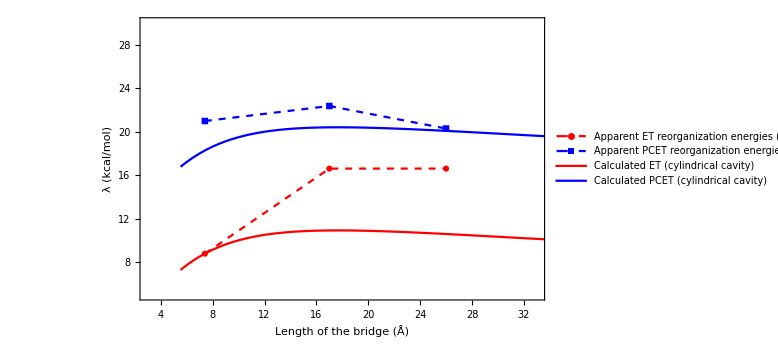

```mathematica
ListPlot[{λETUNCvsL,λPCETUNCvsL,λETcylLtable,λPCETcylLtable},
PlotRange->{{3,33},{5,30}},
BaseStyle->{FontSize->18},
ImageSize->Large,
Axes->False,
Frame->True,
FrameStyle->Directive[Black,Thickness[0.0025]],
PlotMarkers->{Automatic,Automatic,None,None},
Joined->{True,True,True,True},
PlotStyle->{{Red,Dashed},{Blue,Dashed},Red,Blue},
FrameLabel->{"Length of the bridge (Å)","λ (kcal/mol)"},
LabelStyle->{12},
PlotLegends->Placed[
{"Apparent ET reorganization energies (UNC)",
"Apparent PCET reorganization energies (UNC)",
"Calculated ET (cylindrical cavity)",
"Calculated PCET (cylindrical cavity)"},
{0.3,0.85}]
]
```